```mathematica
$Assumptions = {t ∈ Reals, t >0,x ∈ Reals, y ∈ Reals, a ∈ Reals, a >= 0, u ∈ Reals, kx ∈ Reals, ky ∈ Reals, q ∈ Reals,q>=0, θ ∈ Reals}
```

{t∈ℝ,t>0,x∈ℝ,y∈ℝ,a∈ℝ,a≥0,u∈ℝ,kx∈ℝ,ky∈ℝ,q∈ℝ,q≥0,θ∈ℝ}

# Parameters

```mathematica
a = 4 π/3
t = 3*10^4
u = 1/2 10^-3
Δ = 1
α = -I 3 Sqrt[3]/(8 π) a
```

(4 π)/3

30000

1/2000

1

-(ⅈ √3)/2

# Spinor

```mathematica
f =FullSimplify[ComplexExpand[ Exp[I a/Sqrt[3] y] (1 + 2*Exp[-I Sqrt[3]/2 a y] Cos[1/2 a x])]]
```

ⅇ^(-2/9 ⅈ π (3 x+√3 y)) (1+ⅇ^((4 ⅈ π x)/3)+ⅇ^(2/3 ⅈ π (x+√3 y)))

```mathematica
H = FullSimplify[{{u, t Conjugate[f]}, {t f, u}}]
```

{{1/2000,30000 ⅇ^(2/9 ⅈ π (3 x+√3 y)) (1+ⅇ^(-4/3 ⅈ π x)+ⅇ^(-2/3 ⅈ π (x+√3 y)))},{30000 ⅇ^(-2/9 ⅈ π (3 x+√3 y)) (1+ⅇ^((4 ⅈ π x)/3)+ⅇ^(2/3 ⅈ π (x+√3 y))),1/2000}}

```mathematica
rxtemp = FullSimplify[t * (Cos[a/Sqrt[3] y] + 2 Cos[a/(2 Sqrt[3]) y]Cos[a/2 x])]
rytemp= FullSimplify[t*(Sin[a/Sqrt[3] y] - 2 Sin[a/(2 Sqrt[3]) y] Cos[a/2 x])]
rztemp = u
htemp = FullSimplify[ComplexExpand[Sqrt[rxtemp^2+rytemp^2+rztemp^2]]]
```

30000 (2 Cos[(2 π x)/3] Cos[(2 π y)/(3 √3)]+Cos[(4 π y)/(3 √3)])

60000 (-Cos[(2 π x)/3]+Cos[(2 π y)/(3 √3)]) Sin[(2 π y)/(3 √3)]

1/2000

√(10800000000000001/4000000+1800000000 Cos[(4 π x)/3]+1800000000 Cos[2/3 π (x-√3 y)]+1800000000 Cos[2/3 π (x+√3 y)])

```mathematica
x = q * Cos[θ] + 4 π/(3 a)
y = q * Sin[θ]+0
rx = FullSimplify[Normal[Series[rxtemp, {q,0,3}]]]
ry = FullSimplify[Normal[Series[rytemp, {q,0,3}]]]
rz = FullSimplify[Normal[Series[rztemp, {q,0,3}]]]
h = FullSimplify[Normal[Series[htemp, {q,0,3}]]]
```

1+q Cos[θ]

q Sin[θ]

20000/27 π q (√3 (-27+2 π^2 q^2) Cos[θ]+9 π q Cos[2 θ])

20000/27 π q (√3 (27-2 π^2 q^2)+18 π q Cos[θ]) Sin[θ]

1/2000

1/2000+1200000000000 π^2 q^2-(800000000000 π^3 q^3 Cos[3 θ])/(√3)

```mathematica
tempvector = FullSimplify[Normal[Series[1/Sqrt[2 * h * (rz + h)] * {I ry - rx, rz + h},{q,0,3}]]]
```

{20000000/27 π q (-9 ⅇ^(-2 ⅈ θ) π q+√3 ⅇ^(ⅈ θ) (27-48600000000000002 π^2 q^2)),1-600000000000000 π^2 q^2+(400000000000000 π^3 q^3 Cos[3 θ])/(√3)}

```mathematica
FullSimplify[tempvector.Conjugate[tempvector]]
```

1+400000000000000/243 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+1600000000000000/81 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])

```mathematica
nmz = FullSimplify[ComplexExpand[Conjugate[tempvector].tempvector]]
```

1+400000000000000/243 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+1600000000000000/81 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])

```mathematica
FullSimplify[ComplexExpand[vector.Conjugate[vector]]]
```

Sign[243+400000000000000 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+4800000000000000 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])]

```mathematica
vector = FullSimplify[1/Sqrt[nmz]*ComplexExpand[tempvector]]
```

{(20000000 π q (-9 ⅇ^(-2 ⅈ θ) π q+√3 ⅇ^(ⅈ θ) (27-48600000000000002 π^2 q^2)))/(√(729+1200000000000000 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+14400000000000000 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ]))),(9 √3 (1-600000000000000 π^2 q^2)+3600000000000000 π^3 q^3 Cos[3 θ])/(√(243+400000000000000 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+4800000000000000 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])))}

```mathematica
temp1 = FullSimplify[ComplexExpand[Normal[Series[Conjugate[vector].H.vector,{q,0,3}]]]]
```

Series::ztest1: Unable to decide whether numeric quantity 1-(-1)^(1/3)+(-1)^(2/3) is equal to zero. Assuming it is.

(ⅇ^(1/2 ⅈ Arg[243+400000000000000 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+4800000000000000 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])]) (-19440000000000000800000000000000 ⅇ^(-3 ⅈ θ) π^5 q^5+3 √3 (9+400000000000000 π^2 q^2 (-108+48600000000000001 π^2 q^2))+86400000000000000 π^3 q^3 Cos[3 θ]))/(6000 √Abs[243+400000000000000 π^4 q^4 (-2405700000000000081+2361960000000000210600000000000004 π^2 q^2)+4800000000000000 π^5 q^5 (16200000000000001 √3 Cos[3 θ]+1350000000000000 π q Cos[6 θ])])

```mathematica
temp2 = FullSimplify[Normal[Series[First[Eigenvalues[H]],{q,0,3}]]]
```

1/2000+20000 √3 π q-20000/3 π^2 q^2 Cos[3 θ]-(5000 π^3 q^3 (7+Cos[6 θ]))/(9 √3)

```mathematica
FullSimplify[Normal[Series[temp1-temp2, {q,0,1}]]]
```

-20000 √3 π q

```mathematica
q=Sqrt[(kx)^2+(ky)^2]
θ = ArcTan[kx,ky]
```

√(kx^2+ky^2)

ArcTan[kx,ky]

```mathematica
Clear[q, θ,x,y]
```

# Spinor @ κ_1

```mathematica
Subscript[κ, 1]=4 π/(3 a)*{1, 0}
```

{1,0}

```mathematica
kx = First[Subscript[κ, 1]]+q*Cos[θ]
ky=Last[Subscript[κ, 1]]+q*Sin[θ]
```

1+q Cos[θ]

q Sin[θ]

```mathematica
v1 = FullSimplify[ComplexExpand[N[vector]]]
```

{ⅇ^((0.-2. ⅈ) θ) q (-6.57974×10^7 q+ⅇ^((0.+3. ⅈ) θ) (1.08828×10^8-1.93336×10^24 q^2)),1.-5.92176×10^15 q^2+7.16059×10^15 q^3 Cos[3. θ]}

# Spinor @ κ_3

```mathematica
Subscript[κ, 3]=4 π/(3 a)*{Cos[2 π/3], Sin[2 π/3]}
```

{-1/2,(√3)/2}

```mathematica
Clear[kx,ky]
```

```mathematica
kx = First[Subscript[κ, 3]]+q*Cos[θ]
ky=Last[Subscript[κ, 3]]+q*Sin[θ]
```

-1/2+q Cos[θ]

(√3)/2+q Sin[θ]

```mathematica
v3 = FullSimplify[ComplexExpand[N[vector]]]
```

{ⅇ^((0.-2. ⅈ) θ) q (-6.57974×10^7 q+ⅇ^((0.+3. ⅈ) θ) (1.08828×10^8-1.93336×10^24 q^2)),1.-5.92176×10^15 q^2+7.16059×10^15 q^3 Cos[3. θ]}

# Spinor @ κ_5

```mathematica
Subscript[κ, 5]=4 π/(3 a)*{Cos[4 π/3], Sin[4 π/3]}
```

{-1/2,-(√3)/2}

```mathematica
Clear[kx,ky]
```

```mathematica
kx = First[Subscript[κ, 5]]+q*Cos[θ]
ky=Last[Subscript[κ, 5]]+q*Sin[θ]
```

-1/2+q Cos[θ]

-(√3)/2+q Sin[θ]

```mathematica
v5 = FullSimplify[ComplexExpand[N[vector]]]
```

{ⅇ^((0.-2. ⅈ) θ) q (-6.57974×10^7 q+ⅇ^((0.+3. ⅈ) θ) (1.08828×10^8-1.93336×10^24 q^2)),1.-5.92176×10^15 q^2+7.16059×10^15 q^3 Cos[3. θ]}

# 3-Patch Coefficients

```mathematica
ϕ = 0
ϵ =FullSimplify[ComplexExpand[ Sqrt[6]*q*Im[α]]]
delt = FullSimplify[3/2 Δ]
ϵp =FullSimplify[ delt/Sqrt[2]+(ϵ+Sqrt[ϵ^2+delt^2])/Sqrt[2]]
ϵm = FullSimplify[ delt/Sqrt[2]-(ϵ+Sqrt[ϵ^2+delt^2])/Sqrt[2]]
```

0

-(3 q)/(√2)

3/2

3/4 (√2-2 q+√(2+4 q^2))

3/4 (√2+2 q-√(2+4 q^2))

```mathematica
C1m =FullSimplify[ComplexExpand[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ]-ϵm)]]
C3m =FullSimplify[ComplexExpand[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ - 2 π/3]-ϵm)]]
C5m =FullSimplify[ComplexExpand[ 1/Sqrt[2 * Sqrt[ϵ^2+Δt^2]*(ϵ + Sqrt[ϵ^2+Δt^2])] 1/Sqrt[3](2 I Exp[I ϕ] ϵp Sin[θ +2 π/3]-ϵm)]]
```

(√3 ⅇ^(-1/2 ⅈ Arg[-(3 q)/(√2)+√((9 q^2)/2+Δt^2)]) (-1-√2 q+√(1+2 q^2)+2 ⅈ (1-√2 q+√(1+2 q^2)) Sin[θ]))/(2 2^(3/4) (9 q^2+2 Δt^2)^(1/4) (9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^(1/4))

(√3 ⅇ^(-1/2 ⅈ Arg[-(3 q)/(√2)+√((9 q^2)/2+Δt^2)]) (-1-√2 q+√(1+2 q^2)-2 ⅈ (1-√2 q+√(1+2 q^2)) Cos[π/6-θ]))/(2 2^(3/4) (9 q^2+2 Δt^2)^(1/4) (9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^(1/4))

(√3 ⅇ^(-1/2 ⅈ Arg[-(3 q)/(√2)+√((9 q^2)/2+Δt^2)]) (-1-√2 q+√(1+2 q^2)+2 ⅈ (1-√2 q+√(1+2 q^2)) Cos[π/6+θ]))/(2 2^(3/4) (9 q^2+2 Δt^2)^(1/4) (9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^(1/4))

# Important Quantities

```mathematica
C1m2 = FullSimplify[ComplexExpand[Conjugate[C1m] * C1m]]
C3m2 = FullSimplify[ComplexExpand[Conjugate[C3m] * C3m]]
C5m2 = FullSimplify[ComplexExpand[Conjugate[C5m] * C5m]]
```

(6 q (-1+3 √2 q-3 √(1+2 q^2))+3 √2 (3+√(1+2 q^2))-6 (√2-2 q+2 √2 q^2-2 q √(1+2 q^2)+√(2+4 q^2)) Cos[2 θ])/(8 √(9 q^2+2 Δt^2) ((9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^2)^(1/4))

(3 (-2 q+6 √2 q^2-6 q √(1+2 q^2)+√(2+4 q^2)+(2 √2 q^2+√(2+4 q^2)-2 q (1+√(1+2 q^2))) (Cos[2 θ]+√3 Sin[2 θ])+√2 (3+Cos[2 θ]+√3 Sin[2 θ])))/(8 √(9 q^2+2 Δt^2) ((9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^2)^(1/4))

(3 (3 √2-2 q+6 √2 q^2-6 q √(1+2 q^2)+√(2+4 q^2)+(√2-2 q+2 √2 q^2-2 q √(1+2 q^2)+√(2+4 q^2)) Cos[2 θ]-√3 (√2-2 q+2 √2 q^2-2 q √(1+2 q^2)+√(2+4 q^2)) Sin[2 θ]))/(8 √(9 q^2+2 Δt^2) ((9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^2)^(1/4))

```mathematica
dq1 = FullSimplify[D[v1,q]]
dθ1 = FullSimplify[1/q D[v1,θ]]
dq3 = FullSimplify[D[v3,q]]
dθ3 = FullSimplify[1/q D[v3,θ]]
dq5 = FullSimplify[D[v5,q]]
dθ5 = FullSimplify[1/q D[v5,θ]]
```

{-1.31595×10^8 ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) (1.08828×10^8-5.80008×10^24 q^2),q (-1.18435×10^16+2.14818×10^16 q Cos[3. θ])}

{(0.+1.31595×10^8 ⅈ) ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) ((0.+1.08828×10^8 ⅈ)-(0.+1.93336×10^24 ⅈ) q^2),-2.14818×10^16 q^2 Sin[3. θ]}

{-1.31595×10^8 ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) (1.08828×10^8-5.80008×10^24 q^2),q (-1.18435×10^16+2.14818×10^16 q Cos[3. θ])}

{(0.+1.31595×10^8 ⅈ) ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) ((0.+1.08828×10^8 ⅈ)-(0.+1.93336×10^24 ⅈ) q^2),-2.14818×10^16 q^2 Sin[3. θ]}

{-1.31595×10^8 ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) (1.08828×10^8-5.80008×10^24 q^2),q (-1.18435×10^16+2.14818×10^16 q Cos[3. θ])}

{(0.+1.31595×10^8 ⅈ) ⅇ^((0.-2. ⅈ) θ) q+ⅇ^((0.+1. ⅈ) θ) ((0.+1.08828×10^8 ⅈ)-(0.+1.93336×10^24 ⅈ) q^2),-2.14818×10^16 q^2 Sin[3. θ]}

```mathematica
A1θ = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v1].dθ1,{q,0,4}]]]]
A1q = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v1].dq1,{q,0,4}]]]]
A3θ = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v3].dθ3,{q,0,4}]]]]
A3q = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v3].dq3,{q,0,4}]]]]
A5θ = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v5].dθ5,{q,0,4}]]]]
A5q = FullSimplify[ComplexExpand[Normal[Series[Conjugate[v5].dq5,{q,0,4}]]]]
```

q ((0.+1.18435×10^16 ⅈ)-(0.+4.20807×10^32 ⅈ) q^2+q ((0.+7.16059×10^15 ⅈ)-(0.+1.2721×10^32 ⅈ) q^2) Cos[3. θ]+q (5.-2.5442×10^32 q^2) Sin[3. θ])

q (6.-7.7148×10^32 q^2+q (-4.+4.24033×10^32 q^2) Cos[3. θ]+q ((0.+7.16059×10^15 ⅈ)+(0.+1.2721×10^32 ⅈ) q^2) Sin[3. θ])

q ((0.+1.18435×10^16 ⅈ)-(0.+4.20807×10^32 ⅈ) q^2+q ((0.+7.16059×10^15 ⅈ)-(0.+1.2721×10^32 ⅈ) q^2) Cos[3. θ]+q (5.-2.5442×10^32 q^2) Sin[3. θ])

q (6.-7.7148×10^32 q^2+q (-4.+4.24033×10^32 q^2) Cos[3. θ]+q ((0.+7.16059×10^15 ⅈ)+(0.+1.2721×10^32 ⅈ) q^2) Sin[3. θ])

q ((0.+1.18435×10^16 ⅈ)-(0.+4.20807×10^32 ⅈ) q^2+q ((0.+7.16059×10^15 ⅈ)-(0.+1.2721×10^32 ⅈ) q^2) Cos[3. θ]+q (5.-2.5442×10^32 q^2) Sin[3. θ])

q (6.-7.7148×10^32 q^2+q (-4.+4.24033×10^32 q^2) Cos[3. θ]+q ((0.+7.16059×10^15 ⅈ)+(0.+1.2721×10^32 ⅈ) q^2) Sin[3. θ])

```mathematica
q2A1q = FullSimplify[ComplexExpand[Normal[Series[C1m2 * A1q,{q,0,4}]]]]
q2A1θ = FullSimplify[ComplexExpand[Normal[Series[C1m2 * A1θ,{q,0,4}]]]]
q2A3q = FullSimplify[ComplexExpand[Normal[Series[C3m2 * A3q,{q,0,4}]]]]
q2A3θ = FullSimplify[ComplexExpand[Normal[Series[C3m2 * A3θ,{q,0,4}]]]]
q2A5q = FullSimplify[ComplexExpand[Normal[Series[C5m2 * A5q,{q,0,4}]]]]
q2A5θ = FullSimplify[ComplexExpand[Normal[Series[C5m2 * A5θ,{q,0,4}]]]]
```

1/Δt^8 q (Δt^4)^(3/4) (9. (Δt^2)^(3/2)+q (19.0919 Δt^2-1.15722×10^33 q (Δt^2)^(3/2)+q^2 (-42.9567-2.45483×10^33 Δt^2+1.63656×10^33 (Δt^2)^(3/2)))+q (q (-12.7279+18. q) Δt^2-6. (Δt^2)^(3/2)+q (8.+6.3605×10^32 q) (Δt^2)^(3/2)) Cos[3. θ]+q (q ((-2.0679+2.27849×10^16 ⅈ)+(2.92445-3.22227×10^16 ⅈ) q) Δt^2+(0.+1.07409×10^16 ⅈ) (Δt^2)^(3/2)+((0.-1.51899×10^16 ⅈ)+(0.+1.90815×10^32 ⅈ) q) q (Δt^2)^(3/2)) Sin[3. θ]+Cos[2 θ] (-9. (Δt^2)^(3/2)+q (-19.0919 Δt^2+1.15722×10^33 q (Δt^2)^(3/2)+q^2 (42.9567+2.45483×10^33 Δt^2-1.63656×10^33 (Δt^2)^(3/2)))+q ((12.7279-18. q) q Δt^2+6. (Δt^2)^(3/2)+(-8.-6.3605×10^32 q) q (Δt^2)^(3/2)) Cos[3. θ]+q ((-2.85837+3.22227×10^16 ⅈ) q (-0.707107+1. q) Δt^2-(0.+1.07409×10^16 ⅈ) (Δt^2)^(3/2)+((0.+1.51899×10^16 ⅈ)-(0.+1.90815×10^32 ⅈ) q) q (Δt^2)^(3/2)) Sin[3. θ]))

1/Δt^8 q (Δt^4)^(3/4) ((0.+1.77653×10^16 ⅈ) (Δt^2)^(3/2)+q ((-8.+3.76859×10^16 ⅈ) Δt^2-(4.+2.51239×10^16 ⅈ) (Δt^2)^(3/2)+q ((0.-8.47932×10^16 ⅈ) q+((0.-5.32959×10^16 ⅈ)+(3.91641×10^17-1.339×10^33 ⅈ) q) Δt^2-(1.08086×10^17+6.31211×10^32 ⅈ) (Δt^2)^(3/2)+(1.48655×10^17+8.92667×10^32 ⅈ) q (Δt^2)^(3/2)))+q ((11.2226-3.22227×10^16 ⅈ) q (-0.707107+1. q) Δt^2+(0.+1.07409×10^16 ⅈ) (Δt^2)^(3/2)+((0.-1.51899×10^16 ⅈ)-(0.+1.90815×10^32 ⅈ) q) q (Δt^2)^(3/2)) Cos[3. θ]+q ((15.9099-22.5 q) q Δt^2+7.5 (Δt^2)^(3/2)+(-8.-3.8163×10^32 q) q (Δt^2)^(3/2)) Sin[3. θ]+Cos[2 θ] ((0.-1.77653×10^16 ⅈ) (Δt^2)^(3/2)+q ((-8.-3.76859×10^16 ⅈ) Δt^2-(4.-2.51239×10^16 ⅈ) (Δt^2)^(3/2)+q ((0.+8.47932×10^16 ⅈ) q+((0.+5.32959×10^16 ⅈ)+(3.91641×10^17+1.339×10^33 ⅈ) q) Δt^2-(1.08086×10^17-6.31211×10^32 ⅈ) (Δt^2)^(3/2)+(1.48655×10^17-8.92667×10^32 ⅈ) q (Δt^2)^(3/2)))+q ((11.2226+3.22227×10^16 ⅈ) q (-0.707107+1. q) Δt^2-(0.+1.07409×10^16 ⅈ) (Δt^2)^(3/2)+((0.+1.51899×10^16 ⅈ)+(0.+1.90815×10^32 ⅈ) q) q (Δt^2)^(3/2)) Cos[3. θ]+q (q (-15.9099+22.5 q) Δt^2-7.5 (Δt^2)^(3/2)+q (8.+3.8163×10^32 q) (Δt^2)^(3/2)) Sin[3. θ]))

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

# 3P No Spinor Ω

```mathematica
nsA1θ = FullSimplify[ComplexExpand[Conjugate[C1m] *1/q D[C1m, θ]]]
nsA1q = FullSimplify[ComplexExpand[Conjugate[C1m]*D[C1m, q]]]
nsA3θ = FullSimplify[ComplexExpand[Conjugate[C3m]*1/q D[C3m, θ]]]
nsA3q = FullSimplify[ComplexExpand[Conjugate[C3m]*D[C3m, q]]]
nsA5θ = FullSimplify[ComplexExpand[Conjugate[C5m]*1/q D[C5m, θ]]]
nsA5q = FullSimplify[ComplexExpand[Conjugate[C5m]*D[C5m, q]]]
```

(3 Cos[θ] (ⅈ q (√2 q-√(1+2 q^2))+(√2-2 q+2 √2 q^2-2 q √(1+2 q^2)+√(2+4 q^2)) Sin[θ]))/(2 q √(9 q^2+2 Δt^2) ((9 q^2+Δt^2-3 q √(9 q^2+2 Δt^2))^2)^(1/4))

```mathematica
nsΩ1 = FullSimplify[ComplexExpand[I * D[nsA1θ, q] - I * 1/q * D[nsA1q, θ]]]
nsΩ3 = FullSimplify[ComplexExpand[I * D[nsA3θ, q] - I * 1/q * D[nsA3q, θ]]]
nsΩ5 = FullSimplify[ComplexExpand[I * D[nsA5θ, q] - I * 1/q * D[nsA5q, θ]]]
```

1/(3 q^2 (1+2 q^2)^(3/2))√(1+4 q^2-2 q √(2+4 q^2)) Cos[θ] (q (√2+2 q (√(1+2 q^2)+q (√2-2 q-√(2+4 q^2))))-2 ⅈ (1+2 q^2) (1+√(1+2 q^2)+q (√2+2 q+√(2+4 q^2))) Sin[θ])

-((2 q^2 (6 q^2 √(1+2 q^2)+16 q^4 √(1+2 q^2)-(1+2 q^2) (3+q (√2+8 q (1+√2 q)))) Cos[θ]+ⅈ √3 (1+√(1+2 q^2)+q (-3 √2 (1+√(1+2 q^2))-4 q (-3 (1+√(1+2 q^2))+q (5 √2 (1+√(1+2 q^2))+q (-9 (1+√(1+2 q^2))+q (8 q (-1+√2 q-√(1+2 q^2))+√2 (11+8 √(1+2 q^2)))))))) Cos[2 θ]+12 ⅈ q^3 √(2+4 q^2) Cos[π/6+2 θ]+32 ⅈ q^5 √(2+4 q^2) Cos[π/6+2 θ]+2 q √(2+4 q^2) Sin[π/6-θ]+20 q^3 √(2+4 q^2) Sin[π/6-θ]+32 q^5 √(2+4 q^2) Sin[π/6-θ]-12 q^4 √(3+6 q^2) Sin[θ]-32 q^6 √(3+6 q^2) Sin[θ]+2 √3 q^2 (1+2 q^2) (3+q (√2+8 q (1+√2 q))) Sin[θ]-ⅈ √(1+2 q^2) Sin[2 θ]-12 ⅈ q^2 √(1+2 q^2) Sin[2 θ]-36 ⅈ q^4 √(1+2 q^2) Sin[2 θ]-32 ⅈ q^6 √(1+2 q^2) Sin[2 θ]+3 ⅈ q √(2+4 q^2) Sin[2 θ]+20 ⅈ q^3 √(2+4 q^2) Sin[2 θ]+32 ⅈ q^5 √(2+4 q^2) Sin[2 θ]+ⅈ (1+2 q^2)^2 (-1+q (3 √2+8 q (-1+√2 q))) Sin[2 θ])/(6 (q+2 q^3)^2 (1+4 q^2-2 q √(2+4 q^2))^(3/2)))

-((2 q^2 (6 q^2 √(1+2 q^2)+16 q^4 √(1+2 q^2)-(1+2 q^2) (3+q (√2+8 q (1+√2 q)))) Cos[θ]-ⅈ √3 (1+√(1+2 q^2)+q (-3 √2 (1+√(1+2 q^2))-4 q (-3 (1+√(1+2 q^2))+q (5 √2 (1+√(1+2 q^2))+q (-9 (1+√(1+2 q^2))+q (8 q (-1+√2 q-√(1+2 q^2))+√2 (11+8 √(1+2 q^2)))))))) Cos[2 θ]+12 q^4 √(3+6 q^2) Sin[θ]+32 q^6 √(3+6 q^2) Sin[θ]-2 √3 q^2 (1+2 q^2) (3+q (√2+8 q (1+√2 q))) Sin[θ]-ⅈ √(1+2 q^2) Sin[2 θ]-12 ⅈ q^2 √(1+2 q^2) Sin[2 θ]-36 ⅈ q^4 √(1+2 q^2) Sin[2 θ]-32 ⅈ q^6 √(1+2 q^2) Sin[2 θ]+3 ⅈ q √(2+4 q^2) Sin[2 θ]+20 ⅈ q^3 √(2+4 q^2) Sin[2 θ]+32 ⅈ q^5 √(2+4 q^2) Sin[2 θ]+ⅈ (1+2 q^2)^2 (-1+q (3 √2+8 q (-1+√2 q))) Sin[2 θ]+2 q √(2+4 q^2) Sin[π/6+θ]+20 q^3 √(2+4 q^2) Sin[π/6+θ]+32 q^5 √(2+4 q^2) Sin[π/6+θ]-12 ⅈ q^3 √(2+4 q^2) Sin[1/3 (π+6 θ)]-32 ⅈ q^5 √(2+4 q^2) Sin[1/3 (π+6 θ)])/(6 (q+2 q^3)^2 (1+4 q^2-2 q √(2+4 q^2))^(3/2)))

```mathematica
nsΩ = FullSimplify[nsΩ1 + nsΩ3 + nsΩ5]
```

0

# 3P Ω

```mathematica
cΩ1 = FullSimplify[ComplexExpand[I * D[q2A1θ, q] - I * 1/q * D[q2A1q, θ]]]
cΩ3 = FullSimplify[ComplexExpand[I * D[q2A3θ, q] - I * 1/q * D[q2A3q, θ]]]
cΩ5 = FullSimplify[ComplexExpand[I * D[q2A5θ, q] - I * 1/q * D[q2A5q, θ]]]
```

-7.89568×10^15+8.41615×10^32 q^2+q Cos[3. θ] (4.77373×10^15+5.93647×10^32 q^2+(0.+1.92154×10^17 ⅈ) q^2 Cos[θ] Sin[θ])+q ((0.+4.80384×10^16 ⅈ) q^2+(9.54746×10^15+1.69613×10^32 q^2) Sin[2 θ]) Sin[3. θ]+Cos[2 θ] (7.89568×10^15-8.41615×10^32 q^2+q (-4.77373×10^15-5.93647×10^32 q^2) Cos[3. θ]-(0.+4.80384×10^16 ⅈ) q^3 Sin[3. θ])

-7.89568×10^15+8.41615×10^32 q^2+q ((0.+4.80384×10^16 ⅈ) q^2+(8.26834×10^15+(1.46889×10^32+1.80144×10^16 ⅈ) q^2) Cos[2 θ]+(-9.54746×10^15-(1.69613×10^32-5.40432×10^16 ⅈ) q^2) Cos[θ] Sin[θ]) Sin[3. θ]+(-7.89568×10^15+8.41615×10^32 q^2) Sin[π/6+2 θ]+q Cos[3. θ] (4.77373×10^15+5.93647×10^32 q^2+q^2 (2.96823×10^32 Cos[2 θ]+(1.02823×10^33-7.20576×10^16 ⅈ) Cos[θ] Sin[θ])+4.77373×10^15 Sin[π/6+2 θ])

-7.89568×10^15+8.41615×10^32 q^2+q Cos[3. θ] (4.77373×10^15+5.93647×10^32 q^2+(2.38686×10^15+2.96823×10^32 q^2) Cos[2 θ]+(-4.13417×10^15-(5.14113×10^32+3.60288×10^16 ⅈ) q^2) Sin[2 θ])+Cos[1/3 (π+6 θ)] (-7.89568×10^15+8.41615×10^32 q^2+(0.+3.60288×10^16 ⅈ) q^3 Sin[3. θ])+q Sin[3. θ] ((0.+4.80384×10^16 ⅈ) q^2+(-9.54746×10^15-1.69613×10^32 q^2) Sin[1/3 (π+6 θ)])

```mathematica
patchΩ = FullSimplify[cΩ1 + cΩ3 + cΩ5]
```

-2.36871×10^16+2.52484×10^33 q^2+q Cos[3. θ] (1.43212×10^16+(1.78094×10^33+4.5036×10^15 ⅈ) q^2+(-3.+(4.5036×10^16+6.30504×10^16 ⅈ) q^2) Cos[θ] Sin[θ])+q (-1.25-4.5036×10^15 q^2+(9.0072×10^15-1.80144×10^16 ⅈ) q^2 Cos[θ] Sin[θ]) Sin[3. θ]+Cos[2 θ] (-0.25+(2.2518×10^15-5.40432×10^16 ⅈ) q^3 Cos[3. θ]+q (0.25-(2.2518×10^16+9.0072×10^15 ⅈ) q^2) Sin[3. θ])

# Graphene Ω

```mathematica
gq2A1q = FullSimplify[ComplexExpand[Normal[Series[A1q,{q,0,5}]]]]
gq2A1θ = FullSimplify[ComplexExpand[Normal[Series[A1θ,{q,0,5}]]]]
gq2A3q = FullSimplify[ComplexExpand[Normal[Series[A3q,{q,0,5}]]]]
gq2A3θ = FullSimplify[ComplexExpand[Normal[Series[A3θ,{q,0,5}]]]]
gq2A5q = FullSimplify[ComplexExpand[Normal[Series[A5q,{q,0,5}]]]]
gq2A5θ = FullSimplify[ComplexExpand[Normal[Series[A5θ,{q,0,5}]]]]
```

1.12136×10^49 q^5-7.20576×10^16 q^4 Cos[3. θ]+ⅈ q^2 (7.16059×10^15+1.2721×10^32 q^2) Sin[3. θ]

ⅈ q (1.18435×10^16-4.20807×10^32 q^2+3.73788×10^48 q^4+q (7.16059×10^15-1.2721×10^32 q^2) Cos[3. θ])+7.20576×10^16 q^4 Sin[3. θ]

1.12136×10^49 q^5-7.20576×10^16 q^4 Cos[3. θ]+ⅈ q^2 (7.16059×10^15+1.2721×10^32 q^2) Sin[3. θ]

ⅈ q (1.18435×10^16-4.20807×10^32 q^2+3.73788×10^48 q^4+q (7.16059×10^15-1.2721×10^32 q^2) Cos[3. θ])+7.20576×10^16 q^4 Sin[3. θ]

1.12136×10^49 q^5-7.20576×10^16 q^4 Cos[3. θ]+ⅈ q^2 (7.16059×10^15+1.2721×10^32 q^2) Sin[3. θ]

ⅈ q (1.18435×10^16-4.20807×10^32 q^2+3.73788×10^48 q^4+q (7.16059×10^15-1.2721×10^32 q^2) Cos[3. θ])+7.20576×10^16 q^4 Sin[3. θ]

```mathematica
gΩ = FullSimplify[ComplexExpand[I * D[gq2A1θ, q] - I * 1/q * D[gq2A1q, θ]]]
```

-1.18435×10^16+1.26242×10^33 q^2-1.86894×10^49 q^4+q (7.16059×10^15+8.9047×10^32 q^2) Cos[3. θ]

```mathematica
truegΩ = FullSimplify[-u/(2 (q^2+u^2)^(3/2))]
```

-1/(4000 (1/4000000+q^2)^(3/2))

# Comparison Plots

```mathematica
q = 10^-8
```

1/100000000

```mathematica
Plot[{Re[patchΩ],Re[gΩ]}, {θ,0,2*π}, AxesLabel->{"θ", "Ω"}, PlotLegends->{"3-Patch", "Graphene"}]
```

-Graphics-

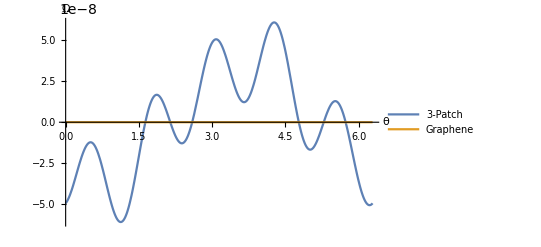

```mathematica
Plot[{Im[patchΩ],Im[gΩ]}, {θ,0,2*π}, AxesLabel->{"θ", "Ω"}, PlotLegends->{"3-Patch", "Graphene"}]
```

```mathematica
Clear[q]
```

# Contour Plots

```mathematica
Clear[x,y]
```

```mathematica
q=Sqrt[x^2+y^2]
θ = ArcTan[x,y]
```

√(x^2+y^2)

ArcTan[x,y]

```mathematica
xlim = 10^-5
ylim = 10^-5
```

1/100000

1/100000

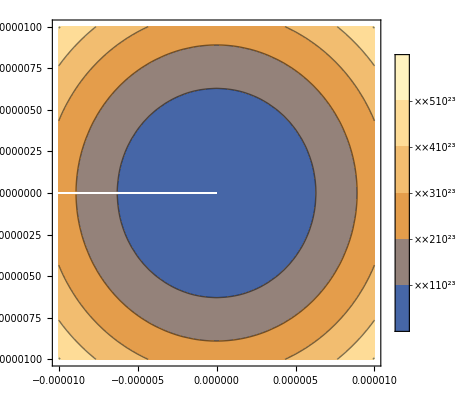

```mathematica
ContourPlot[Re[patchΩ], {x, -xlim, xlim}, {y, -ylim, ylim},PlotLegends->Automatic]
```

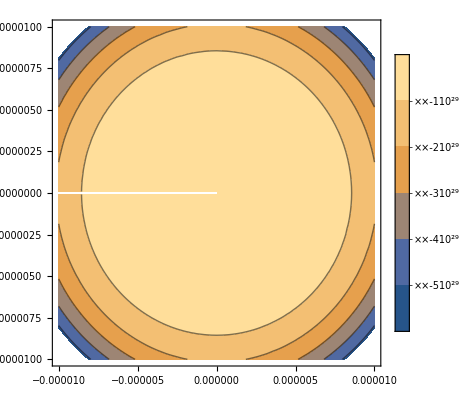

```mathematica
ContourPlot[Re[gΩ], {x, -xlim, xlim}, {y, -ylim, ylim},PlotLegends->Automatic]
```

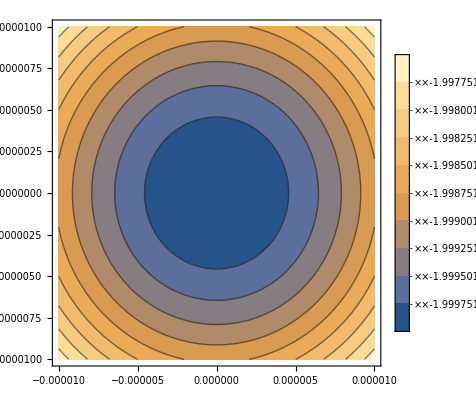

```mathematica
ContourPlot[truegΩ, {x, -xlim, xlim}, {y, -ylim, ylim},PlotLegends->Automatic]
```